#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results

Real32

Experimental results for the total cross section for deuteron photodisintegration
(W. Jaus & W.S. Woolcock -- Nuclear Physics A473 (1987) 685-704)
[σ_tot]=μb=10^-4 fm^2
[Lab photon energy] = MeV

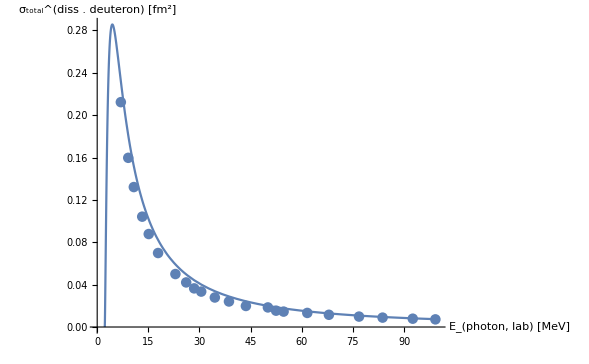

```mathematica
DeutDataMuBarn=ReadList["../../../data/deuteron_diss_tot_exp.dat",Number,RecordLists->True];
DeutDataMuBarn2=ReadList["../../../data/partovi_deuteron_diss_total_mu-barn_phot-lab-MeV.dat",Number,RecordLists->True];
DeutDataFm2=Transpose[{Transpose[DeutDataMuBarn2][[1]],Transpose[DeutDataMuBarn2][[2]] 10.^(-4)}];

σBethe[ω_,E0_,mM_]:=2 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,2.222,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . deuteron) [fm^2]"}],
ListPlot[DeutDataFm2,PlotLabel->Style["Partovi, Approximation I",Orange,22]]]
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0,1,2};
J0=1;
mIns=Range[-#,#,1]&/@Subscript[I, n];

thresholdLIT=10.8^(-9);
thresholdD=thresholdLIT;
```

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_D^n|(Ĥ)_(V18+UIX)|ϕ_D^m ⟩, m,n∈{1,N_D}

```mathematica
DNormHamMat=readREAL8list["./mat_np1^+"];
DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}];
```

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,0.2];
```

min/max: {6.13566×10^-6,7.5583}

(min/max) discarded elements: 24 {6.13566×10^-6,0.184427}

#### The real calculation

Set a sensible cut-off

min/max: {6.13566×10^-6,7.5583}

(min/max) discarded elements: 0 {∞,-∞}

B(D) = -2.23063

Dim_full^deuteron = 40=^!40   ;     Dim_(non - singular)^deuteron = 40

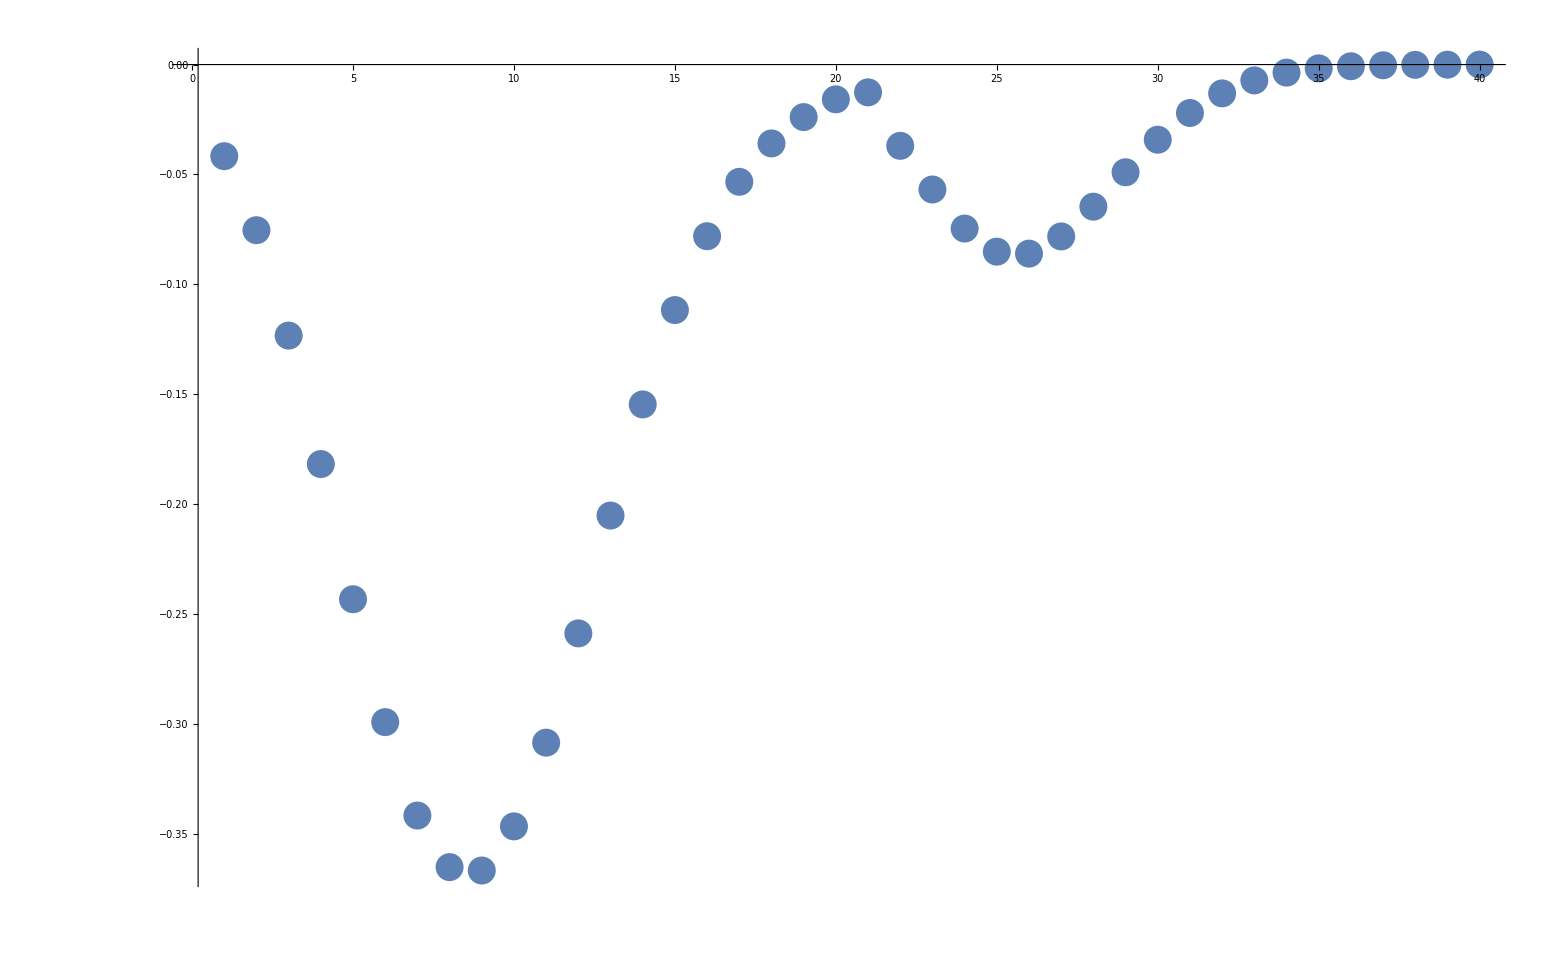

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,thresholdD];

{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[DNmhi].DHam.DNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["B(D) = ",e0];
Print["Dim_full^deuteron = ",Dimensions[DNorm][[1]],"=^!",DBasisDim,"   ;     Dim_(non - singular)^deuteron = ",Dimensions[v0][[1]]]
fullv0=Normalize[Transpose[DNmh].v0];
ListPlot[Re[fullv0],PlotRange->Full]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = {36,36,36}

min/max: {2.16893×10^-11,11.1626}

(min/max) discarded elements: 3 {2.16893×10^-11,2.04214×10^-10}

J=0:  E_0=0.00953493

min/max: {2.16893×10^-11,11.1626}

(min/max) discarded elements: 3 {2.16893×10^-11,2.04214×10^-10}

J=1:  E_0=0.00953499

min/max: {2.16893×10^-11,11.1626}

(min/max) discarded elements: 3 {2.16893×10^-11,2.04214×10^-10}

J=2:  E_0=0.0095349

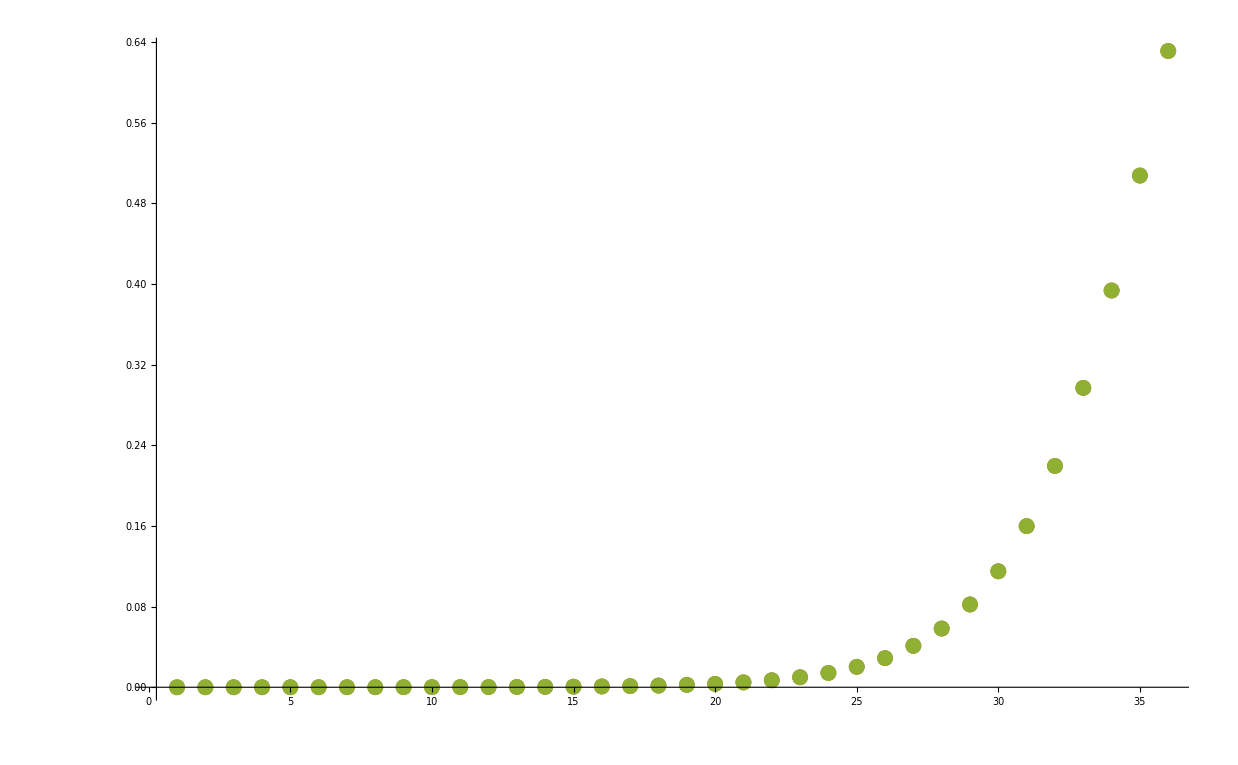

```mathematica
LitNmhis={};
fullv0l={};
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
AppendTo[LitNmhis,{LitNmh,LitNmhi}];
{e0l,v0l}=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,Normalize[Transpose[LitNmh].v0l]];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

ListPlot[Re[fullv0l],PlotRange->Full]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],1,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

CouplingBlocks={};
Do[
Print["m_L=",mL];
If[Sign[mIn]>=0,mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],1,"0"],mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],2,"0"]];
If[Sign[mL]>=0,mMUL=StringPadRight[StringDelete[ToString[mL],"."],1,"0"],mMUL=StringPadRight[StringDelete[ToString[mL],"."],2,"0"]];

files="./"<>ToString[#]<>"_S_"<>JLIT<>"_"<>mJLIT<>"_"<>mMUL<>".lit"&/@ks;
inhomos=readREAL8list[#]&/@files;
CouplingMatrices=ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]&/@inhomos;
CouplingBloxx=#[[DBasisDim+1;;,;;DBasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
coupl=ClebschGordan[{multipolarity,mL},{J0,mIn-mL},{Subscript[I, n][[nj]],mIn}];
(*Print["⟨",multipolarity,mL,J0,mIn-mL,"|",Subscript[I, n][[nj]],mIn,"⟩ =  ",coupl];*)
(*Print[ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}]//MatrixForm];*)
AppendTo[CouplingBlocks,coupl ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}]];
,{mL,mM}
];

tmp =BinaryReadList["InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt,"Real32"];
OutDim=Dimensions[tmp][[1]]/DBasisDim;
test=ArrayReshape[tmp,{OutDim,DBasisDim}];
AppendTo[CouplingBlockT,{mIn,test}];
AppendTo[CouplingBlock,{mIn,Total[CouplingBlocks]}];
If[Select[Flatten[Total[CouplingBlocks]/test],#!=1.&]≠{},
Print["m_I_n=",mIn,"  : ",Total[CouplingBlocks]/test//MatrixForm]];
,{mIn,mIns[[nj]]}]

AppendTo[CouplingBlockj,CouplingBlockT];
,{nj,Range[1,Length[Subscript[I, n]]]}]

Print["Dim(⟨ψ|ο̂|deuteron⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

m_L=-1

m_L=0

m_L=1

m_I_n=0  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=-1

m_L=0

m_I_n=-1  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=-1

m_L=1

m_I_n=0  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=0

m_L=1

m_I_n=1  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=-1

m_I_n=-2  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=-1

m_L=0

m_I_n=-1  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=-1

m_L=0

m_L=1

m_I_n=0  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=0

m_L=1

m_I_n=1  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

m_L=1

m_I_n=2  : (1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

Dim(⟨ψ|ο̂|deuteron⟩) = {3,36,40}

Dim(⟨ψ|Ĥ|ψ⟩) = {3,36,36}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {3,36,36}

#### Analysis of RHS

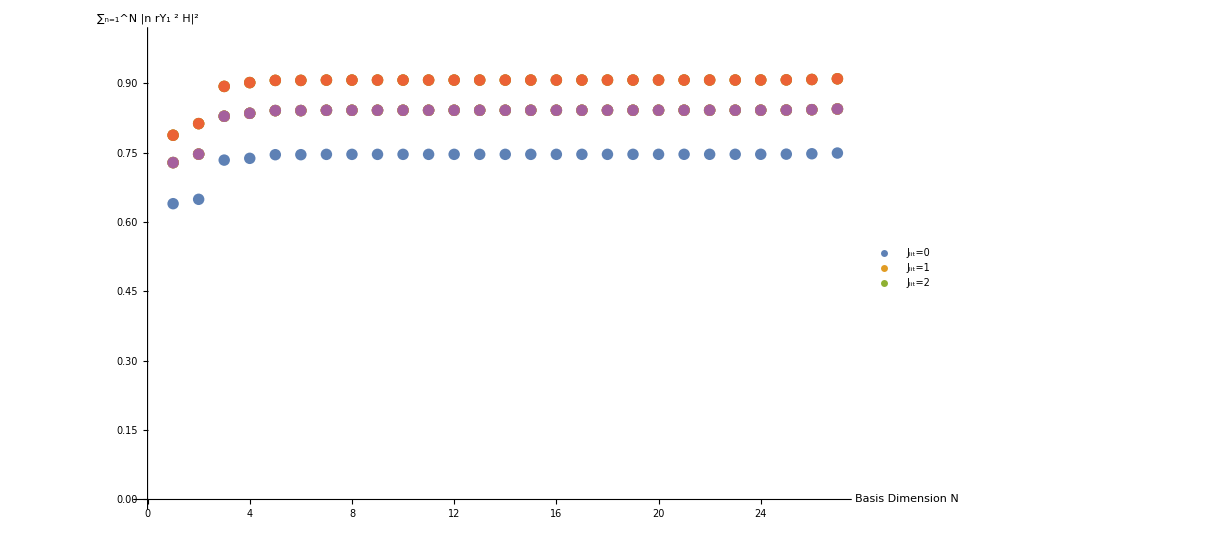

```mathematica
thrs=10^(-7);
OμRHS=normreg[thrs,DNorm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
inhomo={};
Do[
Do[
OμLHS=normreg[thrs,LitNorm[[nj]]];
{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].LitHam[[nj]]).OμLHS];
tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[inhomo,(Transpose[OμLHS].(tmp.OμRHS)).evgs];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
mm=1;
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
inhomonorms=Table[Norm[#[[;;n]]],{n,Length[#]}]&/@inhomo;
ListPlot[inhomonorms,AxesLabel->{"Basis Dimension N","∑_(n=1)^N |n rY_1^2 H|^2"},PlotLegends->lege,ImageSize->ImgSize,PlotRange->{Automatic,{0,1}}]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=4.0;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
```

```mathematica
Clear[normreg];
normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],#[[1]]>threshold&]];
(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];

Clear[decompose];
decompose[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:= Block[{OμRHS,λsD,trfD,OμLHS,λfinal,trfLit,inhomo,egs,evgs},
OμRHS=normreg[thresholdD,DNorm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
egs=Min[λsD];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];

OμLHS=normreg[thresholdLIT,LITNorm];

{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].LITHam).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λfinal]];

inhomo=(Transpose[OμLHS].(LITYD.OμRHS)).evgs;
{λfinal,(trfLit.inhomo)^2,egs}
];

Clear[litcomp];
litcomp[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:=
Block[
{λscf=decompose[thresholdD,thresholdLIT,DNorm,DHam,LITNorm,LITHam,LITYD]},
egrnd=λscf[[3]];
tmpp=Transpose[λscf[[;;2]]];
Plus@@((#[[2]]/(Abs[#[[1]]-egrnd-σRe]^2+σI^2))&/@tmpp)
];
```

```mathematica
Clear[LIT,LITs,testfu];

minth=thresholdLIT;maxth=.02 thresholdLIT;nth=1;
If[nth==1,thresholdrng={thresholdLIT},thresholdrng=Range[minth,maxth,(maxth-minth)/nth]];

LITsj={};

Do[
testfu={};
Print["I_n=",Subscript[I, n][[nj]]];
Do[

tmp=CouplingBlockj[[nj]][[mm]][[2]];

AppendTo[testfu,(-1)^(Subscript[I, n][[nj]]-J0) Evaluate[litcomp[#,#,DNorm,DHam,LitNorm[[nj]],LitHam[[nj]],tmp]&/@thresholdrng]];

,{mm,Length[mIns[[nj]]]}
];

AppendTo[LITsj,Total[testfu]/.σRe->σRs];
,{nj,Range[1,Length[Subscript[I, n]]]}
]

thrlegend=("λ_𝟙="<>ToString[#,TraditionalForm]&/@thresholdrng);
pltlabs="I_n="<>ToString[#]&/@Subscript[I, n]

plote=ListPlot[Flatten[(Transpose[{σRs,#}]&/@LITsj[[#]])&/@Range[1,Length[Subscript[I, n]]],1],
PlotLabel->Style["σ_I = "<>ToString[σI]<>"    ; J_lit = "<>ToString[Subscript[I, n]],18,Red],
AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},
PlotLegends->Placed[thrlegend,Above],
LabelStyle->12,ImageSize->ImgSize,PlotRange->Full,PlotLabels->pltlabs,
Mesh->5,MeshFunctions->{#2&,#2&,#2&},PlotMarkers->{Automatic,Scaled[0.01 #]}&/@Range[1,nth],
Joined->True];
Export["plot.pdf",plote,"PDF","AllowRasterization"->False]
```

I_n=0

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

I_n=1

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

I_n=2

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

«2 more identical outputs»

{I_n=0,I_n=1,I_n=2}

plot.pdf

note on energies:
the energy of the outgoing, i.e., the eigen-states of Ĥ in the basis with quantum numbers set by the perturbation ⊗ target, states, λ_f,
must equal E_0+ω_lab

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

E_0( th=5.00249×10^-10 ) = -2.23063    dim(D,LIT) = {40}{33}

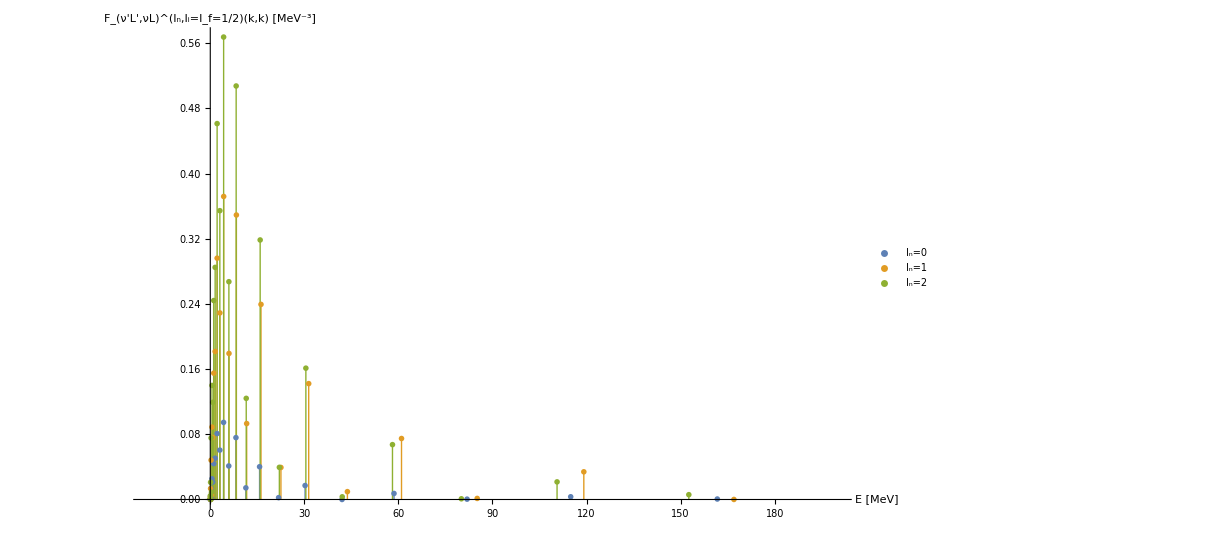
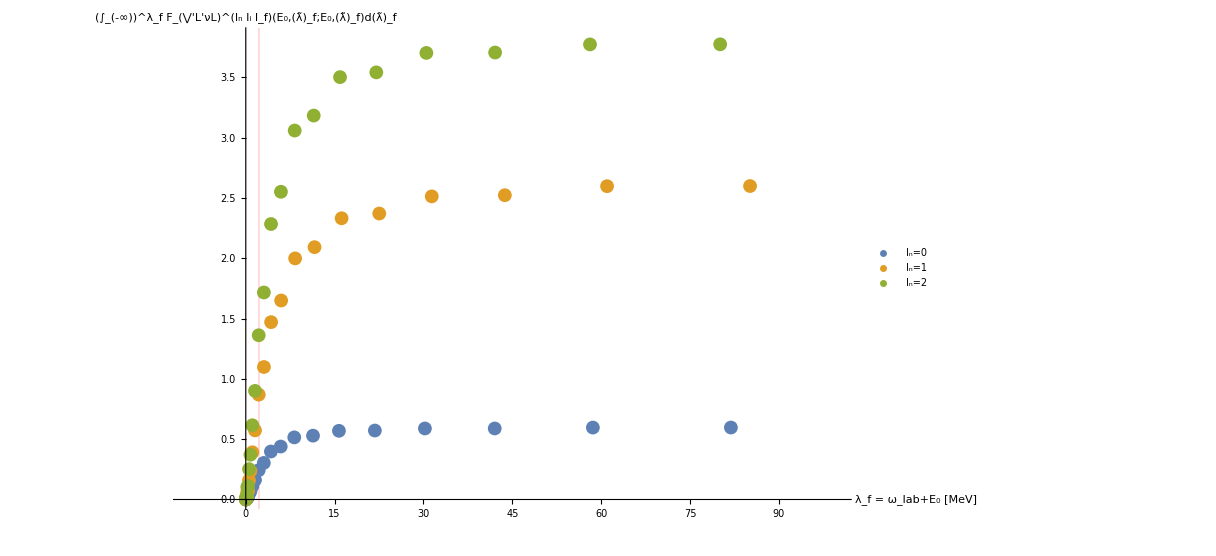

delta_strength_function_deuteron.pdf

```mathematica
Clear[thresh,es,μ,transf];
lpsis={};CumStrengths={};

es=Eigensystem[DNorm];
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>thresholdD&]];
OμRHS=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
egs=Min[λsD];
leg={};

Do[
lpsi={};
esl=Eigensystem[LitNorm[[nj]]];
{μl,transfl}=Transpose[Select[Transpose[esl],Re[#[[1]]]>thresholdLIT&]];
OμLHS=(Transpose[transfl].DiagonalMatrix[μl^(-1/2)]);
{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].(LitHam[[nj]])).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λfinal]];

tmpl=0;

Do[
inhomo=(Transpose[OμLHS].(CouplingBlockj[[nj]][[mm]][[2]].OμRHS)).(evgs);
(*AppendTo[lpsi,Transpose[{λfinal(*+Abs[egs]*),(trfLit.inhomo)^2}]];*)
tmpl = tmpl + (trfLit.inhomo)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsis,Transpose[{λfinal,tmpl}]];
AppendTo[CumStrengths,Transpose[{Sort[lpsis[[nj]]][[All,1]],Accumulate[Sort[lpsis[[nj]]][[All,2]]]}]];

AppendTo[leg,"I_n="<>ToString[Subscript[I, n][[nj]]]];

(*AppendTo[lpsis,Flatten[lpsi,1]];*)

,{nj,Range[1,Length[Subscript[I, n]]]}
]


plote3=Grid[{{
ListPlot[lpsis,Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{{-20,200},Full},AxesLabel->{Style["E [MeV]",18],Style["F_(ν'L',νL)^(I_n,I_i=I_f=1/2)(k,k) [MeV^-3]",18]},PlotStyle->{},PlotLegends->leg,ImageSize->ImgSize]
},{
ListPlot[CumStrengths,Joined->False,ImageSize->ImgSize,PlotRange->{{-10,100},Automatic},PlotLegends->leg,GridLines->{{{Abs[e0],Red},{Abs[e0l],Red}},None},AxesLabel->{Style["  λ_f = ω_lab+E_0 [MeV]",18],Style["(∫_(-∞))^λ_f F_(⋁'L'νL)^(I_n I_i I_f)(E_0,(λ̃)_f;E_0,(λ̃)_f)d(λ̃)_f",18]}]
}}]
Save[tmpDir<>"/lpsis.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],lpsis]
Save[tmpDir<>"/CumStrength.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],CumStrengths]
Export["delta_strength_function_deuteron.pdf",plote3,"PDF","AllowRasterization"->False]
```

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengths,LocalObject["CumDeuteronStrengths"]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumDeuteronStrengths]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 2500 iterations.

NonlinearModelFit::infeas: Possible infeasibility detected. Returning the best solution found.

{(0.605707 t^6+1.83496 t^5+0.322598 t^4+0.43858 t^3+0.102266 t^2+0.)/(1. t^6+3.41573 t^5+14.148 t^4+8.31166 t^3+4.51993 t^2+2.25293 t+0.0000230713),(2.66388 t^6+33.3297 t^5+20.3633 t^4+23.2477 t^3+14.4041 t^2+0.)/(1. t^6+13.7814 t^5+52.7176 t^4+72.1374 t^3+58.94 t^2+77.1748 t+0.000419105),(3.83388 t^6+18.1984 t^5+0.35432 t^4+33.5943 t^3+7.42276 t^2+0.)/(1. t^6+5.25475 t^5+25.5168 t^4+0.42277 t^3+54.8557 t^2+30.8349 t+0.000391526)}

{Piecewise[{{(-4.44089×10^-16 t^11+0.23397 t^10+16.4716 t^9+37.2323 t^8+35.155 t^7+24.6907 t^6+15.0773 t^5+2.55937 t^4+1.86445 t^3+0.175566 t^2-0.00386133 t+0.0000192173)/((-1. t^6-3.35852 t^5-13.9866 t^4-7.77515 t^3-4.28986 t^2-2.16895 t+0.0210546)^2), t≥0.00953493}, {0, True}}],Piecewise[{{(3.3824 t^10+239.818 t^9+1962.59 t^8+4587.79 t^7+6257.93 t^6+10803.7 t^5+4522.08 t^4+3405.9 t^3+1011.67 t^2-20.2256 t+0.0978829)/((-1. t^6-13.7242 t^5-52.0619 t^4-70.1392 t^3-56.9052 t^2-76.0703 t+0.730146)^2), t≥0.00953499}, {0, True}}],Piecewise[{{(-3.55271×10^-15 t^11+1.94767 t^10+194.762 t^9+349.861 t^8+446.552 t^7+2581.15 t^6+1756.12 t^5+1785.26 t^4+2002.03 t^3+170.663 t^2-3.801 t+0.0189761)/((-1. t^6-5.19754 t^5-25.2676 t^4+0.54567 t^3-54.8575 t^2-29.7889 t+0.28863)^2), t≥0.0095349}, {0, True}}]}

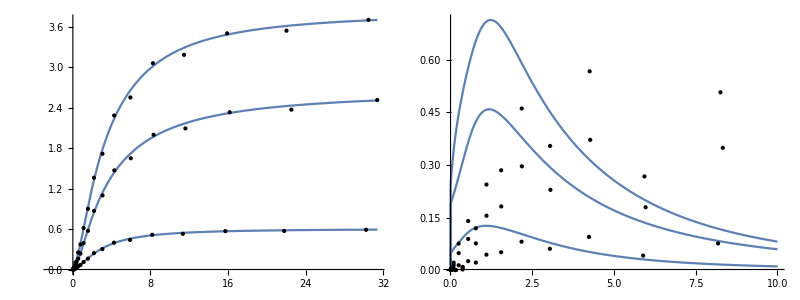

```mathematica
data=CumStrengths;
dataShifted=Transpose[{#[[All,1]]-#[[All,1]][[1]],#[[All,2]]}]&/@CumStrengths;
ordnum=6;orddenom=ordnum-1;
coffs={Array[cnum,ordnum],Array[cdenom,orddenom+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.0001,0.2},Length[Flatten[coffs]]]}];

(*num=Sum[coffs[[1]][[n]] (t)^n,{n,ordnum}]&/@Range[Length[data]];
denom=1+Sum[coffs[[2]][[n]] (t)^n,{n,orddenom}]&/@Range[Length[data]];*)
offsets=Min[#[[All,1]]]&/@data;
num=Sum[coffs[[1]][[n]] (t-0 #)^n,{n,2,ordnum}]&/@offsets;
denom=1+coffs[[2]][[-1]] t^ordnum+Sum[coffs[[2]][[n]] (t-0 #)^n,{n,orddenom}]&/@offsets;

model=num/denom;
constr=#>10.2^(-2)&/@Flatten[coffs];(*10.1^2>#>10.2^(-2)&/@Flatten[coffs];*)
constraints=Union[constr,{Abs[coffs[[1]][[-1]]/coffs[[2]][[-1]]-data[[#]][[-1]][[2]]]<10.^(-9)}]&/@Range[Length[data]];

wgts=Flatten[Join[{Differences[data[[#]]][[All,2]][[1]],Differences[data[[#]]][[All,2]]}]]&/@Range[Length[data]];
splitPoint=5;
origFac=121.;
tailFac=121.;

wgt2=Join[origFac #[[;;splitPoint]],#[[1+splitPoint;;-splitPoint]],tailFac #[[-splitPoint+1;;]]]&/@wgts;

optPOSsol=
NonlinearModelFit[dataShifted[[#]],{model[[#]],constraints[[#]]},inicoffs,t,Weights->wgt2[[#]],MaxIterations->2500]&/@Range[Length[data]];

CumFit[ee_]:=Piecewise[ {{optPOSsol[[#]][ee-offsets[[#]]],ee≥offsets[[#]]},{0,ee<offsets[[#]]}}]&/@Range[Length[optPOSsol]]
StC[em_]:=Piecewise[{{D[optPOSsol[[#]][t],t]/.t->(em-offsets[[#]]),em>=offsets[[#]]},{0,em<offsets[[#]]}}]&/@Range[Length[data]]

Simplify[#[t]]&/@optPOSsol//TraditionalForm
Simplify[#]&/@StC[t]//TraditionalForm

percPlot =0.01;
Grid[{{
Plot[CumFit[t-0 offsets[[#]]][[#]]&/@Range[Length[data]],{t,Min[offsets],percPlot Max[#[[All,1]][[-1]]&/@data]},Epilog->{PointSize[Small],Point[#]&/@CumStrengths},PlotRange->{{-2.3,percPlot Max[#[[All,1]][[-1]]&/@data]},{0,Automatic}},ImageSize->ImgSize],
Plot[StC[e2],{e2,Min[offsets],10},Epilog->Map[Point,lpsis],PlotRange->Full,ImageSize->ImgSize]
}}]
```

#### σ_tot=(2π)^2 α·E_γ ∑_(J,M) JM OverHat[E1](J_0 m_0)^2

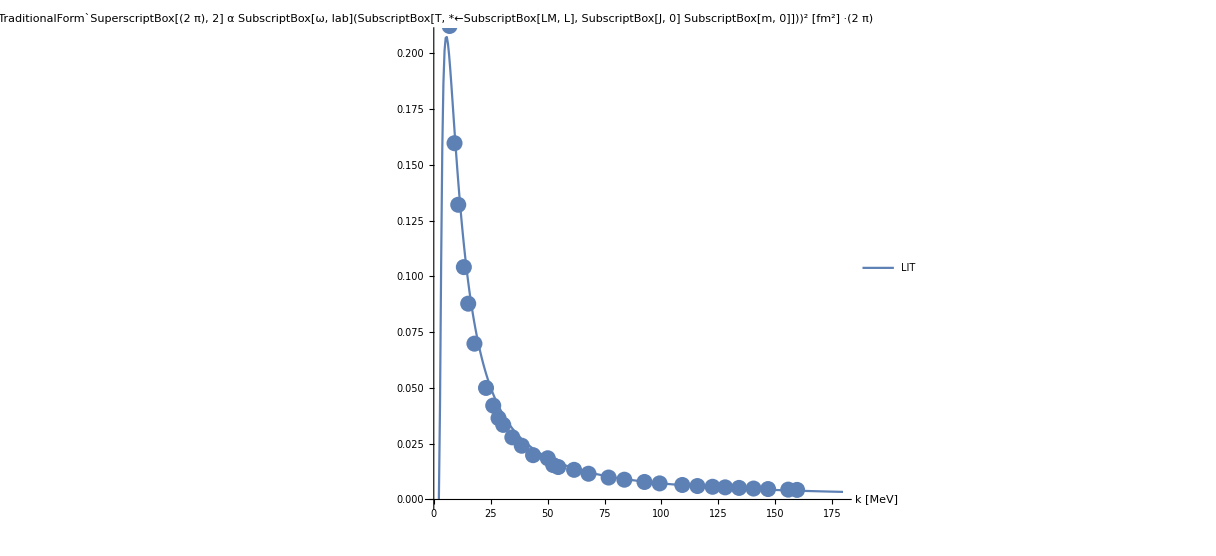
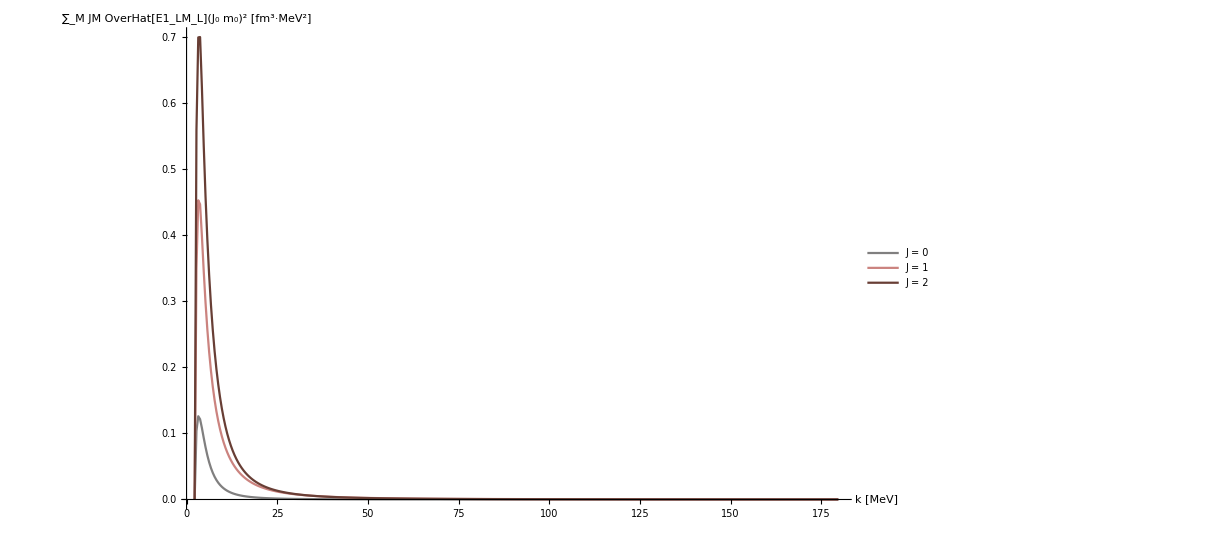
-Graphics- | -Graphics-

```mathematica
Clear[ee,e2];
k0=0.001;k1=180;dK=0.5;
Subscript[k, lab]=Range[Abs[e0],k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;

labelj=("J = "<>ToString[#])&/@Subscript[I, n];
responseListJ=StC[t];
strengthfunctionList=Table[Table[(responseListJ[[nJ]]/.t->ee)/.ee->(e0+kmag),{kmag,Subscript[k, lab]}],{nJ,Range[1,Length[Subscript[I, n]]]}];

z=List[];

For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,(
atmp=ListLinePlot[strengthfunctionList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","FormBox[RowBox[{UnderscriptBox[\"∑\", \"M\"], RowBox[{TemplateBox[{\"JM\"},\"Bra\"], OverscriptBox[SubscriptBox[\"E1\", SubscriptBox[\"LM\", \"L\"]], \"^\"], SuperscriptBox[TemplateBox[{RowBox[{SubscriptBox[\"J\", \"0\"], SubscriptBox[\"m\", \"0\"]}]},\"Ket\"], \"2\"]}]}],TraditionalForm] [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];

Tsquared[Mf_,Mi_,λf_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,
compo=strengthfunctionList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
ampli+=compo;
];
];];
Return[ampli]
]
fudgi=2 Pi;

kinfac=fudgi (2 Pi)^2 Subscript[α, fine] (Subscript[k, lab]+e0)/hbarc;

DissCross[Mf_,Mi_,λf_,kinfac_]:=kinfac Tsquared[Mf,Mi,λf,θ];
lf=1;

Grid[{{
Show[ListPlot[Re[DissCross[Jf,Ji,lf,kinfac]],PlotRange->{Automatic,Full},LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`SuperscriptBox[(2  π), 2] α SubscriptBox[ω, lab](SubscriptBox[T, *←SubscriptBox[LM, L], SubscriptBox[J, 0] SubscriptBox[m, 0]]))^2 [fm^2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotLegends->{"LIT"}],
ListPlot[DeutDataFm2,PlotLegends->"σ_tot data"]],
Show[z,PlotRange->All]
}}]
```